```mathematica
SetDirectory[NotebookDirectory[]]
```

E:\Git\VM2D\build\Airfoils\Generators\Blasius

```mathematica
Dat=Drop[Drop[Import["blas528Rev.txt","Table"],3],-6];
```

```mathematica
bg=Dat[[All,2;;3]];
```

```mathematica
en=Dat[[All,4;;5]];
```

```mathematica
kt=Dat[[All,6;;7]];
```

```mathematica
born=Dat[[All,8;;9]];
```

```mathematica
nm=Dat[[All,10;;11]];
```

```mathematica
ks=Dat[[All,12;;13]];
```

```mathematica
lb=Dat[[All,15]]
```

{0.19509,0.55557,0.83147,0.980785,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.980785,0.83147,0.55557,0.19509,-0.19509,-0.55557,-0.83147,-0.980785,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-0.980785,-0.83147,-0.55557,-0.19509}

```mathematica
rb=Dat[[All,16]]
```

{0.00390181,0.00390181,0.00390181,0.00390181,0.00382813,0.00382812,0.00382813,0.00382813,0.00382813,0.00382812,0.00382813,0.00382813,0.00382812,0.00382813,0.00382813,0.00382813,0.00382812,0.00382813,0.00382813,0.00382813,0.00382812,0.00382813,0.00382813,0.00382812,0.00382813,0.00382813,0.00382812,0.00382813,0.00382813,0.00382813,0.00382813,0.00382812,0.00382813,0.00382813,0.00382812,0.00382813,0.00382813,0.00382812,0.00382813,0.00382813,0.00382812,0.00382813,0.00382812,0.00382813,0.00382813,0.00382812,0.00382813,0.00382813,0.00382812,0.00382813,0.00382813,0.00382812,0.00382813,0.00382813,0.00382812,0.00382813,0.00382812,0.00382813,0.00382813,0.00382812,0.00382813,0.00382813,0.00382812,0.00382813,0.00382813,0.00382812,0.00382813,0.00382812,0.00382812,0.00382812,0.00382813,0.00382813,0.00382813,0.00382812,0.00382813,0.00382813,0.00382812,0.00382813,0.00382813,0.00382813,0.00382812,0.00382813,0.00382813,0.00382813,0.00382812,0.00382813,0.00382813,0.00382812,0.00382813,0.00382813,0.00382813,0.00382812,0.00382813,0.00382813,0.00382812,0.00382813,0.00382813,0.00382813,0.00382812,0.00382813,0.00382813,0.00382812,0.00382813,0.00382813,0.00382813,0.00382812,0.00382813,0.00382813,0.00382812,0.00382813,0.00382813,0.00382813,0.00382812,0.00382813,0.00382813,0.00382812,0.00382813,0.00382813,0.00382813,0.00382812,0.00382813,0.00382813,0.00382813,0.00382812,0.00382813,0.00382813,0.00382812,0.00382813,0.00382813,0.00382813,0.00382812,0.00382813,0.00382813,0.00382812,0.00382813,0.00382812,0.00382813,0.00382812,0.00382813,0.00382812,0.00382812,0.00382813,0.00382812,0.00382812,0.00382813,0.00382812,0.00382812,0.00382813,0.00382812,0.00382812,0.00382813,0.00382812,0.00382813,0.00382812,0.00382812,0.00382813,0.00382812,0.00382812,0.00382813,0.00382812,0.00382812,0.00382813,0.00382812,0.00382813,0.00382812,0.00382812,0.00382813,0.00382812,0.00382812,0.00382813,0.00382812,0.00382812,0.00382813,0.00382812,0.00382812,0.00382813,0.00382812,0.00382813,0.00382812,0.00382812,0.00382813,0.00382812,0.00382812,0.00382813,0.00382812,0.00382812,0.00382813,0.00382812,0.00382812,0.00382813,0.00382812,0.00382813,0.00382812,0.00382812,0.00382813,0.00382812,0.00382812,0.00382813,0.00382812,0.00382812,0.00382813,0.00382812,0.00382813,0.00382812,0.00382812,0.00382813,0.00382812,0.00382812,0.00382813,0.00382812,0.00382812,0.00382813,0.00382812,0.00382812,0.00382813,0.00382812,0.00382813,0.00382812,0.00382812,0.00382813,0.00382812,0.00382812,0.00382813,0.00382812,0.00382812,0.00382813,0.00382812,0.00382812,0.00382813,0.00382812,0.00382813,0.00382812,0.00382812,0.00382813,0.00382812,0.00382812,0.00382813,0.00382812,0.00382812,0.00382813,0.00382812,0.00382813,0.00382812,0.00382812,0.00382813,0.00382812,0.00382812,0.00382813,0.00382812,0.00382812,0.00382813,0.00382812,0.00382812,0.00382813,0.00382812,0.00382813,0.00382812,0.00382812,0.00382813,0.00382812,0.00390181,0.00390181,0.00390181,0.00390181,0.00390181,0.00390181,0.00390181,0.00390181,0.00382813,0.00382812,0.00382813,0.00382813,0.00382813,0.00382812,0.00382813,0.00382813,0.00382812,0.00382813,0.00382813,0.00382813,0.00382812,0.00382813,0.00382813,0.00382813,0.00382812,0.00382813,0.00382813,0.00382812,0.00382813,0.00382813,0.00382812,0.00382813,0.00382813,0.00382813,0.00382813,0.00382812,0.00382813,0.00382813,0.00382812,0.00382813,0.00382813,0.00382812,0.00382813,0.00382813,0.00382812,0.00382813,0.00382812,0.00382813,0.00382813,0.00382812,0.00382813,0.00382813,0.00382812,0.00382813,0.00382813,0.00382812,0.00382813,0.00382813,0.00382812,0.00382813,0.00382812,0.00382813,0.00382813,0.00382812,0.00382813,0.00382813,0.00382812,0.00382813,0.00382813,0.00382812,0.00382813,0.00382812,0.00382812,0.00382812,0.00382813,0.00382813,0.00382813,0.00382812,0.00382813,0.00382813,0.00382812,0.00382813,0.00382813,0.00382813,0.00382812,0.00382813,0.00382813,0.00382813,0.00382812,0.00382813,0.00382813,0.00382812,0.00382813,0.00382813,0.00382813,0.00382812,0.00382813,0.00382813,0.00382812,0.00382813,0.00382813,0.00382813,0.00382812,0.00382813,0.00382813,0.00382812,0.00382813,0.00382813,0.00382813,0.00382812,0.00382813,0.00382813,0.00382812,0.00382813,0.00382813,0.00382813,0.00382812,0.00382813,0.00382813,0.00382812,0.00382813,0.00382813,0.00382813,0.00382812,0.00382813,0.00382813,0.00382813,0.00382812,0.00382813,0.00382813,0.00382812,0.00382813,0.00382813,0.00382813,0.00382812,0.00382813,0.00382813,0.00382812,0.00382813,0.00382812,0.00382813,0.00382812,0.00382813,0.00382812,0.00382812,0.00382813,0.00382812,0.00382812,0.00382813,0.00382812,0.00382812,0.00382813,0.00382812,0.00382812,0.00382813,0.00382812,0.00382813,0.00382812,0.00382812,0.00382813,0.00382812,0.00382812,0.00382813,0.00382812,0.00382812,0.00382813,0.00382812,0.00382813,0.00382812,0.00382812,0.00382813,0.00382812,0.00382812,0.00382813,0.00382812,0.00382812,0.00382813,0.00382812,0.00382812,0.00382813,0.00382812,0.00382813,0.00382812,0.00382812,0.00382813,0.00382812,0.00382812,0.00382813,0.00382812,0.00382812,0.00382813,0.00382812,0.00382812,0.00382813,0.00382812,0.00382813,0.00382812,0.00382812,0.00382813,0.00382812,0.00382812,0.00382813,0.00382812,0.00382812,0.00382813,0.00382812,0.00382813,0.00382812,0.00382812,0.00382813,0.00382812,0.00382812,0.00382813,0.00382812,0.00382812,0.00382813,0.00382812,0.00382812,0.00382813,0.00382812,0.00382813,0.00382812,0.00382812,0.00382813,0.00382812,0.00382812,0.00382813,0.00382812,0.00382812,0.00382813,0.00382812,0.00382812,0.00382813,0.00382812,0.00382813,0.00382812,0.00382812,0.00382813,0.00382812,0.00382812,0.00382813,0.00382812,0.00382812,0.00382813,0.00382812,0.00382813,0.00382812,0.00382812,0.00382813,0.00382812,0.00382812,0.00382813,0.00382812,0.00382812,0.00382813,0.00382812,0.00382812,0.00382813,0.00382812,0.00382813,0.00382812,0.00382812,0.00382813,0.00382812,0.00390181,0.00390181,0.00390181,0.00390181}

```mathematica
Pt=Table[{bg[[i]],en[[i]]},{i,Length[Dat]}];
```

```mathematica
Nrm=Table[{kt[[i]],kt[[i]]+0.1 nm[[i]]},{i,Length[Dat]}];
```

```mathematica
Kas=Table[{kt[[i]],kt[[i]]+0.1 ks[[i]]},{i,Length[Dat]}];
```

```mathematica
contour=ListLinePlot[Pt,PlotStyle->{Blue}];
```

```mathematica
points=ListPlot[Pt,PlotStyle->{{Blue,PointSize[0.005]}}];
```

```mathematica
kontr=ListPlot[kt,PlotStyle->{{Red,PointSize[0.005]}}];
```

```mathematica
bornp=ListPlot[born,PlotStyle->{{Green,PointSize[0.005]}}];
```

```mathematica
normals=ListLinePlot[Nrm,PlotStyle->{Black}];
```

```mathematica
tau=ListLinePlot[Kas,PlotStyle->{Black}];
```

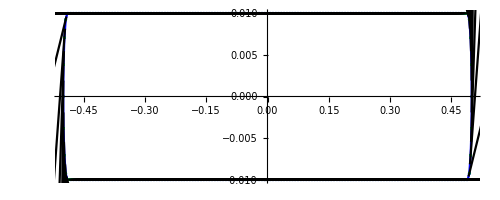

```mathematica
Show[contour,points,bornp,tau,AspectRatio->Automatic]
```

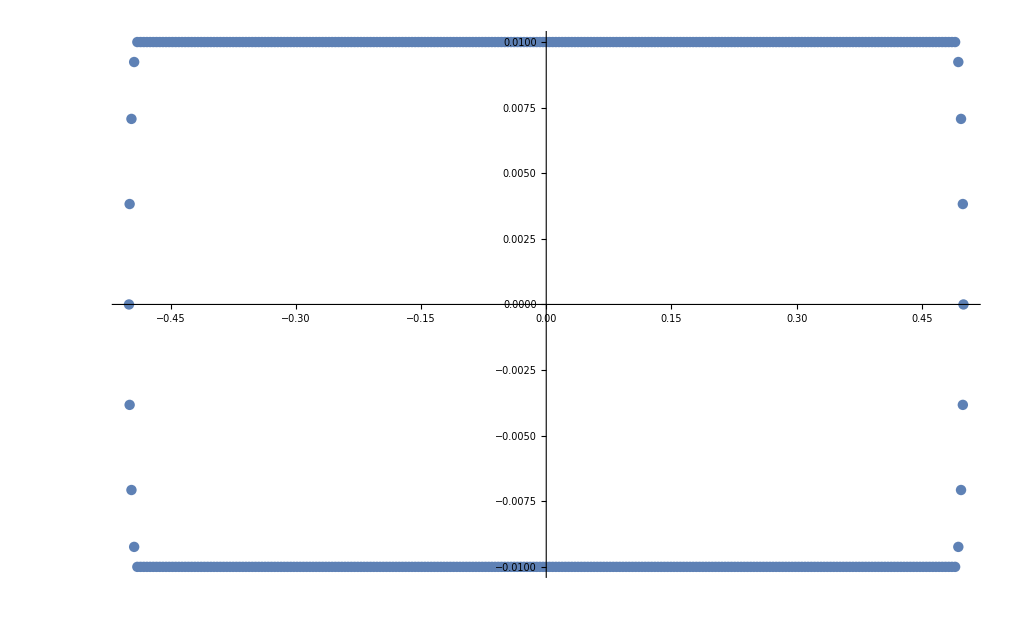

```mathematica
ListPlot[Dat[[All,2;;3]]]
```